A note about seeding:
Although the random initial param values are chosen before simulation (based on the seed), GSL’s numerically methods may use RNG and affect numerics for each iteration and between re-simulations. Therefore, repeating a call to Variational3SATSolver with the same seed but a different maxIterations may change the behaviour of each re-simulation.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
assoc=Get["wickSATdata.txt"];
```

```mathematica
Keys @ assoc // TableForm
```

simRepetitions
maxIterations
derivAccuracy
matrNoise
wrapParams
timeStep
numBools
numParams
solProbEvos
expectedEnergyEvos
initParams
paramEvos
haltIterations
groundReached
hamilType

```mathematica
Manipulate[
	Column @ {
		ListLinePlot[
			assoc["paramEvos"][[rep]],
			PlotLabel-> "parameters",
			GridLines -> {{assoc["haltIterations"][[rep]]}, {}},
			GridLinesStyle-> Directive[Dashed, Gray]
		],
		ListLinePlot[
			assoc["expectedEnergyEvos"][[rep]], 
			PlotLabel -> "<E>",
			PlotRange-> {{0, Automatic},If[assoc["hamilType"] === "DIAGONAL" ,All, {0, -8}]},
			GridLines-> {
			{assoc["haltIterations"][[rep]]}, 
			If[assoc["hamilType"] === "DIAGONAL",Range @ Max@ assoc["spectrum"], {-7.88098231483}]},
			GridLinesStyle-> {Directive[Dashed, Gray], If[assoc["hamilType"] === "DIAGONAL",Gray,Directive[Dashed,Gray]]}
		],
		Sequence @@ If[
			assoc["hamilType"] === "DIAGONAL",
			{
			ListLogPlot[
				assoc["solProbEvos"][[rep]], 
				PlotLabel-> "Prob(sol)",
				PlotStyle->Red,
				PlotRange-> {0,1},
				Joined -> True,
				GridLines -> {{assoc["haltIterations"][[rep]]}, {}},
				GridLinesStyle-> Directive[Dashed, Gray]
			],
			ListLogPlot[
				assoc["specEvos"][[rep]],
				Joined -> True,
				PlotLabel-> "spectrum", 
				PlotRange-> {10^-10, 1},
				PlotStyle -> ReplacePart[
					ConstantArray[
						Directive[Dashed, Thickness@0.005], 
						assoc["spectrumSize"]],
					Position[assoc["spectrum"], 0.][[1,1]] -> Red
				]
			],
			ListPlot[
				Transpose @ {assoc["spectrum"], assoc["spectrumDegeneracy"]},
				AxesLabel-> {"E", "degeneracy"},
				RotateLabel->True,
				Filling -> Axis
			]
			}
		]
	},
	{rep, 1, assoc["simRepetitions"], 1},
	Paneled-> False
]
```

Part::partw: Part 4 of assoc[paramEvos] does not exist.

Part::partw: Part 4 of assoc[haltIterations] does not exist.

ListLinePlot::lpn: assoc[paramEvos]⟦4⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Part::partw: Part 4 of assoc[expectedEnergyEvos] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

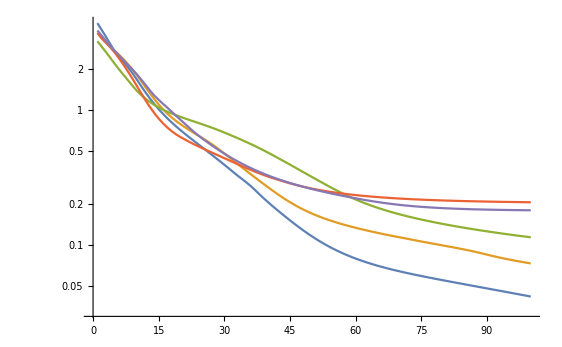

```mathematica
ListLogPlot[
	assoc["expectedEnergyEvos"] + 7.88098231483,
	Joined -> True,
	GridLinesStyle->Directive[Gray, Dashed]
]
```